```mathematica
(* generate pairs of random numbers, keeping those only within the circle *)
n=40000;
ranlist1=Table[{0,0},{i,1,n}];
i=1;
dropped=0;
While[i<=n,
x=2Random[]-1;
y=2Random[]-1;
If[x^2+y^2≤1,
ranlist1[[i]]={x,y};
i+=1;
,
dropped+=1;
];
];
Print[dropped/(n+dropped)*100//N,"% pairs were dropped"]
Print["area outside of circle is ",100(1-π/4)//N,"%"]
```

21.1092% pairs were dropped

area outside of circle is 21.4602%

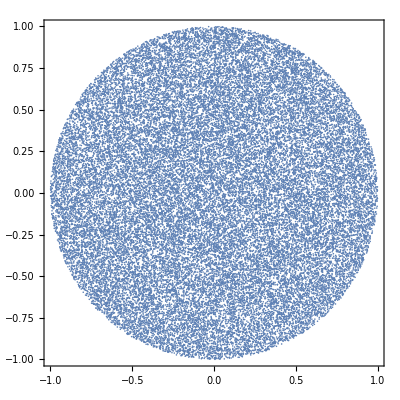

```mathematica
ListPlot[ranlist1,PlotRange->All,AspectRatio->1,Frame->True,Axes->False]
```

```mathematica
(* that was inefficient, lets be clever!  Use polar coordinates to generate a random distance between 0-1 and and random angle between -π to π *)
n=40000;
ranlist2=Table[{0,0},{i,1,n}];
i=1;
While[i<=n,
r=Random[];
θ=π(2Random[]-1);
ranlist2[[i]]={r Cos[θ],r Sin[θ]};
i+=1;
];
```

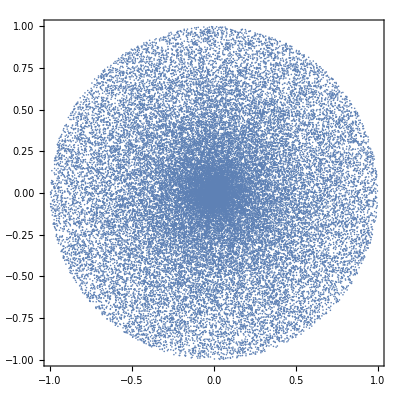

```mathematica
ListPlot[ranlist2,PlotRange->All,AspectRatio->1,Frame->True,Axes->False]
```

```mathematica
(* that didn't work very well.  The problem is the density of states is greater close to the origin.  We must rescale the distance by Sqrt[Random] *)
n=40000;
ranlist3=Table[{0,0},{i,1,n}];
i=1;
While[i<=n,
r=Sqrt[Random[]];
θ=π(2Random[]-1);
ranlist3[[i]]={r Cos[θ],r Sin[θ]};
i+=1;
];
```

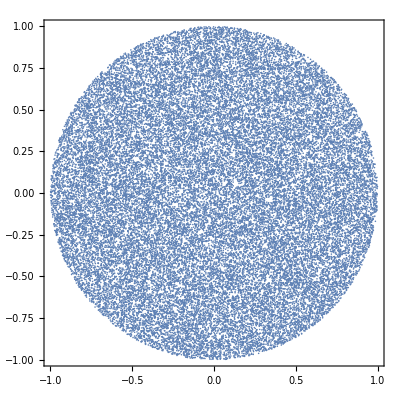

```mathematica
ListPlot[ranlist3,PlotRange->All,AspectRatio->1,Frame->True,Axes->False]
```

```mathematica
(* in 2D, this is called disk point picking.  In 3D, called sphere point picking. *)
```

```mathematica
(* 2D element has volume element 

d(r^2)dθ

both elements of which should be chosen to be uniform.  

*)
```

```mathematica
(* for sphere point picking, the volume element is

d(r^3) d(cos[θ]) dφ

*)
```

```mathematica
n=10000;
ranlist4=Table[{0,0,0},{i,1,n}];
ranlist5=Table[{0,0,0},{i,1,n}];
i=1;
While[i<=n,
r=1;  (* surface of a sphere (easy for visualization *)
θ=π(2Random[]-1); (* uniform angle *)
φ=π(2Random[]-1);  (* uniform angle *)
ranlist4[[i]]={r Sin[θ]Sin[φ],r Sin[θ] Cos[φ],r Cos[θ]};


r=1;
c=2Random[]-1;  (* uniform choice for cos(θ) *)
s=Sqrt[1-c^2];  (* compute sine *)
θ=π(2Random[]-1);  (* uniform angle *)
ranlist5[[i]]={r s Sin[φ],r s  Cos[φ],r c};
i+=1;
];
```

```mathematica
GraphicsGrid[
{{ListPointPlot3D[ranlist4,Boxed->False,Axes->False,BoxRatios->Automatic,ViewPoint->{5,5,5},PlotLabel->"uniform on angle"],
ListPointPlot3D[ranlist5,Boxed->False,Axes->False,BoxRatios->Automatic,ViewPoint->{5,5,5},PlotLabel->"uniform on cosine"]}}
,ImageSize->1000,Spacings->{-150,0}]
```

-Graphics-